## Install Dependencies

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"install_dep.m"}]];
```

```mathematica
InstallMongoDBLink[]
```

Installed MongoDBLink to /Library/Mathematica/Applications

## Run

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

found performanceid = 59ff5bbaca60cc4a4bafcf79

found performanceid = 59ff5ef5ca60cc6cc32e7e8d

found performanceid = 59ff624fca60cca557a77788

found performanceid = 59ff662fca60ccc9ec4ef19a

found performanceid = 59ff6a1cca60ccf42b7273fe

found performanceid = 59ff6d8bca60cc1f3bf1f7c8

found performanceid = 59ff7126ca60cc44f7538b2c

found performanceid = 59ff8a9eca60cc0f07693d1f

found performanceid = 59ff9b72ca60cca0856998c1

found performanceid = 59ff9c45008c59605d65564c

found performanceid = 59ff9c52ca60ccaa907a204b

found performanceid = 59ff9cc9008c5960b0d8a662

found performanceid = 59ff9d44ca60ccb3a047d1b6

found performanceid = 59ff9d58008c5960fee8cff4

found performanceid = 59ff9df7008c596156b9206b

found performanceid = 59ff9e40ca60ccbd5fc12c52

found performanceid = 59ff9ed4008c5961a72e73cc

found performanceid = 59ff9f71ca60ccc7cdd11cd1

found performanceid = 59ff9fb5008c5961f90a106e

found performanceid = 59ffa0a5ca60ccd3d7bb23bb

found performanceid = 59ffa0a7008c5962586b539a

found performanceid = 59ffa1a8008c5962adfb2891

found performanceid = 59ffa207ca60cce009a6c62e

found performanceid = 59ffa377ca60ccee76ca48e3

```mathematica
$AccuracyInformation
```

{<|Model→BVLC-AlexNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.00146,Top5→0.00678|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.00146,Top5→0.00678|>}

### Top1 / Top5 Model Accuracy on AMD64 for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

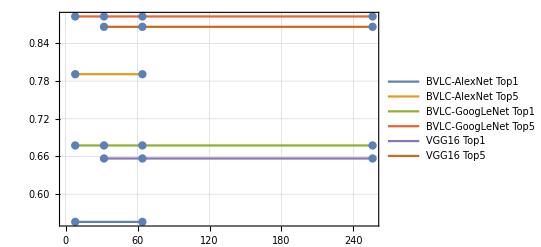

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

### Top1 / Top5 Model Accuracy on AMD64 & Minsky for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

-Graphics-

### Top1 / Top5 Model Accuracy on Minsky for Caffe2

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

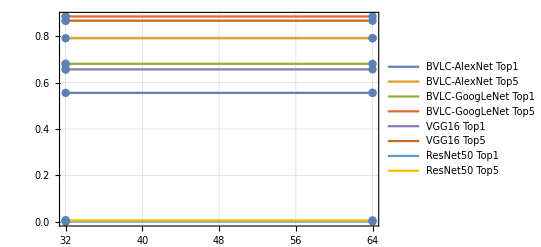

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Joined->True,
Mesh->All,
PlotTheme->"Detailed"
]
```

```mathematica
BarChart[
Catenate[
KeyValueMap[
Function[{key,val},
Join[
Table[<|ToString[e["BatchSize"]] <> " Top1"->Callout[e["Top1"],key <> " Top1"]|>,{e,val}],
Table[<|ToString[e["BatchSize"]] <> " Top5"->Callout[e["Top5"],key <> " Top5"]|>,{e,val}]
]
],
models
]],
ChartLabels->{32,64},
ChartLegends->Automatic,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
Dataset[models]
```

Dataset[<>]

### Model Timing on Minsky for Caffe2

```mathematica
$DurationInformation;
```

```mathematica
Length[$DurationInformation]
```

24

```mathematica
models=GroupBy[$DurationInformation,Lookup["FrameworkModel"]];
```

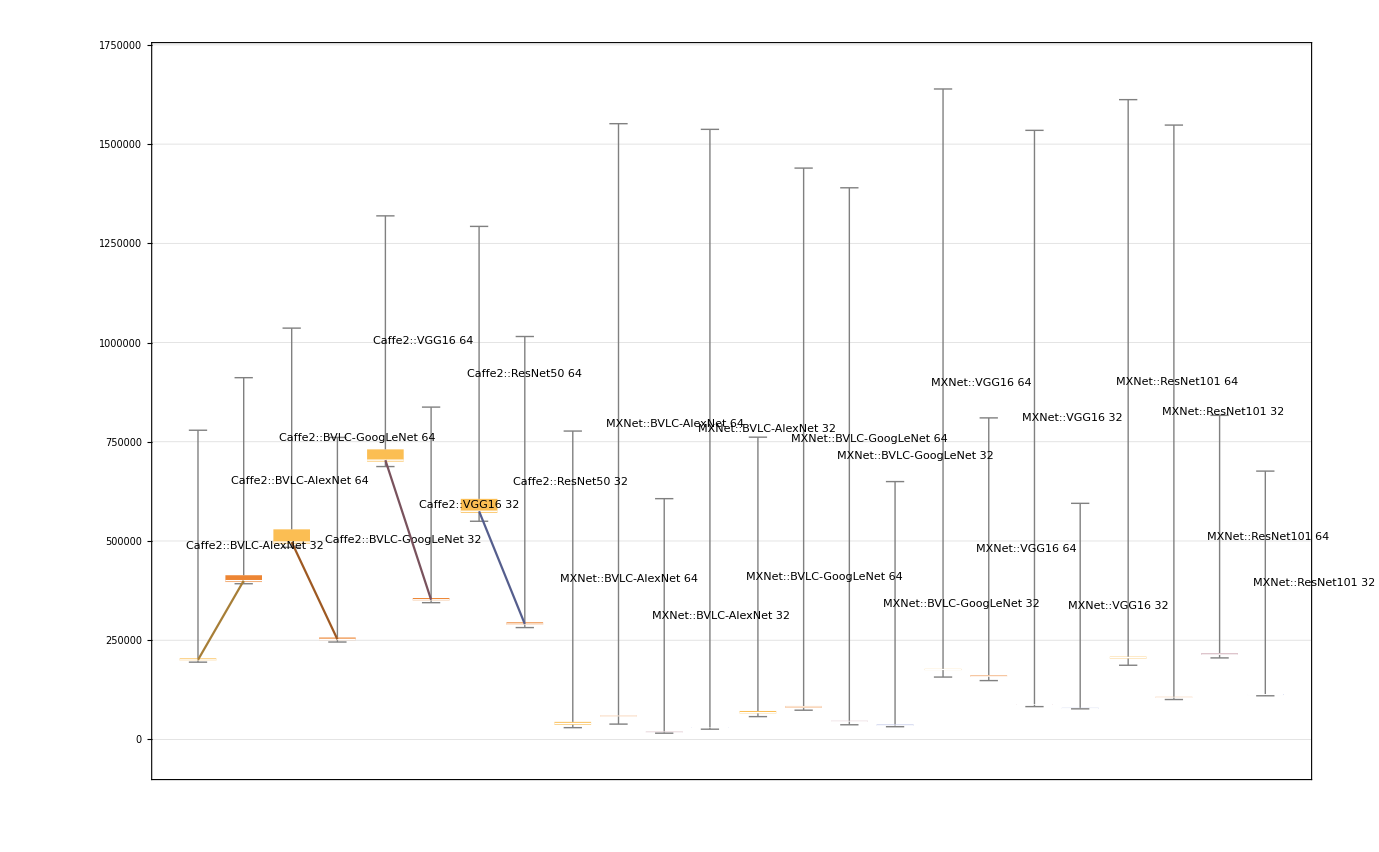

```mathematica
BoxWhiskerChart[
KeyValueMap[
Function[{key,val},
Table[
Labeled[e["Durations"],key <>" " <>ToString[e["BatchSize"]],Left,RotateLabel->True],
{e,val}
]
],
models
],
Joined->True,
LabelingFunction->Automatic,
PlotTheme->"Detailed"
]
```

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
Callout[{e["BatchSize"],Median[e["Durations"]]/e["BatchSize"]},
e["HostName"]<>"::"<>e["Framework"]<>"::"<>ToString[e["BatchSize"]]
],
{e,SortBy[val,#["BatchSize"]&]}
],
key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (us)"}
]
```

-Graphics-

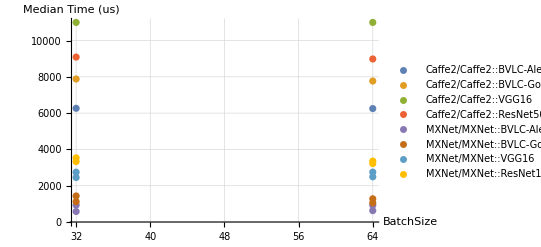

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
Tooltip[{e["BatchSize"],Median[e["Durations"]]/e["BatchSize"]},
GeneralUtilities`Infobox[
<|
"HostName"->e["HostName"],
"MachineArchitecture"->e["MachineArchitecture"],
"UsingGPU"->e["UsingGPU"],
"BatchSize"->e["BatchSize"]
|>,
"Information"
]
],
{e,SortBy[val,#["BatchSize"]&]}
],
First[val]["Framework"]<> "/"<>key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (us)"}
]
```

### Model Timing on Minsky for Caffe2

```mathematica
performanceid=$Evaluations[[-2]]["performanceid"]
```

59fea7ddca60cc31e0f7067a

```mathematica
perf=Association[First[FindDocuments[performanceCollection,{"_id"->performanceid},"Limit"->1]]];
trace=GeneralUtilities`ToAssociations[perf["trace"]]["traces"];
```

```mathematica
getSpans[span_]:=If[KeyExistsQ[span,"spans"],Join[{span},Catenate[getSpans/@span["spans"]]],{span}];
```

```mathematica
trace//Length
```

1

```mathematica
spans=Flatten[getSpans[#["spans"]]&/@trace];
predictSpans=Select[spans,#["operationname"]==="Predict"&];
```

```mathematica
durations=N[Lookup[predictSpans,"duration"]];
```

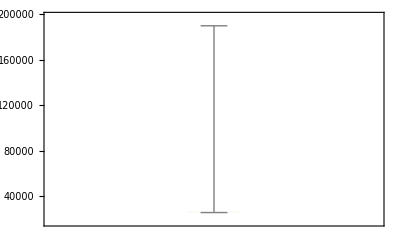

```mathematica
BoxWhiskerChart[durations]
```

```mathematica
Keys[Association[Association[trace]["traces"]]]
```

{traceid,spans,processes,warnings}

```mathematica
Association[
```

```mathematica
Keys[Association[trace]]
```

{traces,total,limit,offset,errors}

```mathematica
a=Dataset[trace];
```

```mathematica
Head[a]
```

Dataset

```mathematica
Dataset
```

```mathematica
GeneralUtilities`ToAssociations[trace]
```

<|traces→{<|traceid→30ab619f593463f0,spans→{<|traceid→30ab619f593463f0,spanid→6a93f66119d92744,parentspanid→,7,processid→p1,process→Null,warnings→{}|>,781,<|1|>},1,warnings→{}|>},3,errors→1|>
 |  |  |  |

```mathematica
........
```

```mathematica
Association[Dataset[trace]]//Keys
```

Keys[Association[Dataset[trace]]]

```mathematica
spans=Catenate[getSpans/@Association[trace]["data"]]
```

traces→{{traceid→30ab619f593463f0,spans→{{traceid→30ab619f593463f0,spanid→6a93f66119d92744,parentspanid→,flags→0,6,processid→p1,process→Null,warnings→{}},781,{1}},1,warnings→{}}}
 |  |  |  |

```mathematica
.
```

```mathematica
CountDocuments[performanceCollection]
```

9